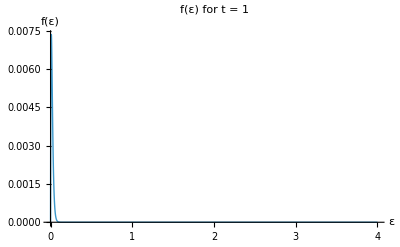

```mathematica
(*Define the function*)f[epsilon_,t_]:=2*Sinh[epsilon]*Exp[1/2*epsilon^2-epsilon*t]

(*Plot for a specific t value,e.g.,t=1*)
Plot[f[epsilon,100],{epsilon,0,4},PlotLabel->"f(ε) for t = 1",AxesLabel->{"ε","f(ε)"},PlotRange->All,PlotStyle->Thick]
```